```mathematica
Clear["Global`*"]
```

```mathematica
r[t_] = {3Cos[3.3π*t], Sin[4π*t] + 4*t};
```

```mathematica
track =ParametricPlot[r[t], {t, 0, 1}, AxesLabel-> {Style["x", Bold], Style["y", Bold]}, PlotRange->All, ImageSize->Full];
```

Find the location of the Pont; where the course crosses itself.

```mathematica
bridge = t/.FindRoot[{r[t] == r[s]},{t,0}, {s, 0.5}] (* grab the t value found from FindRoot. s would work as well. *)
```

0.134804

```mathematica
cauchy = Graphics[{EdgeForm[Thin],Style[Disk[r[0], 0.05], Green]}]; 
laplace = Graphics[{EdgeForm[Thin],Style[Disk[r[1], 0.05], Red]}];
pont = Graphics[{EdgeForm[Thin],Style[Disk[r[bridge], 0.05], Orange]}];
```

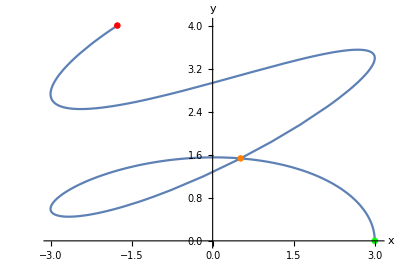

```mathematica
Show[track, cauchy, laplace, pont]
```

Speed is just the magnitude of the velocity vector at a given time, t.

```mathematica
v[t_] = r'[t];
```

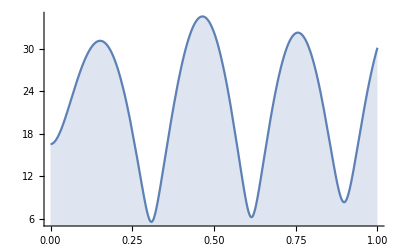

```mathematica
Plot[Norm[v[t]], {t, 0, 1}, Filling->Axis] (* Speed plot *)
```

The average speed is the distanced travelled (arc length 0->1) over the time it took (1hr).
Integrate the scalar magnitude of r[t] from t = 0->1 and devide by 1 hour.

```mathematica
NIntegrate[Norm[v[t]], {t, 0, 1}] (* 22.0332 km/hr *)
```

22.0332

(3.)
Distance between Cauchy and Laplace.

```mathematica
dbt = EuclideanDistance[r[0],r[1]] (* 6.22009 km | dbt = distance between towns *)
```

6.22009

(4.)
1km to each end pt.

```mathematica
kmpt[t_?NumericQ] := NIntegrate[Norm[v[s]], {s, 0, t}];
FindRoot[kmpt[t] == 1, {t, 0}]
FindRoot[kmpt[t] ==((NIntegrate[Norm[v[t]], {t, 0, 1}]) -1), {t, 0}] (* The end point is the length of the curve - 1km. So integrating r'[t] over the interval is the length, and r'[t] = v[t] *)
```

{t→0.0543758}

{t→0.962242}

```mathematica
kmfirstlocation = t/.FindRoot[kmpt[t] == 1, {t, 0}];
kmsecondlocation = t/.FindRoot[kmpt[t] ==((NIntegrate[Norm[v[t]], {t, 0, 1}]) -1), {t, 0}];
kmstart = Graphics[{EdgeForm[Thin], Style[Disk[r[kmfirstlocation], 0.03], Blue]}];
kmend = Graphics[{EdgeForm[Thin], Style[Disk[r[kmsecondlocation], 0.03], Blue]}];
```

(5.)
Curvature = ||T’(t)|| / ||r’(t)||
T’(t) = r’(t) / ||r’(t)||, but r’(t) = v(t)

```mathematica
T[t_] = v[t]/Norm[v[t]];
K[t_] = Norm[T'[t]]/Norm[v[t]];
```

```mathematica
curvature = Plot[K[t], {t, 0, 1}];
Show[curvature]
```

-Graphics-

(6.)
Normal component of acceleration... Norm[v’[t]] == Norm[a[t]]

```mathematica
a[t_] = v'[t];
```

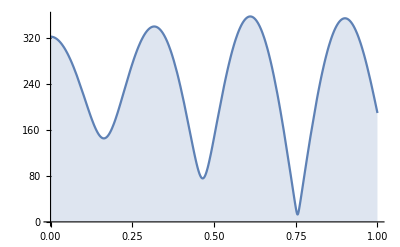

```mathematica
aplot = Plot[Norm[a[t]], {t,0,1}, Filling->Axis];
Show[aplot]
```

(7.)
Maximum normal acceleration will occur at the peaks.

```mathematica
FindMaximum[{Norm[a[t]], 0 ≤ t ≤ 1}, {t,0.2}]
FindMaximum[{Norm[a[t]], 0 ≤ t ≤ 1}, {t,0.8}]
```

{357.586,{t→0.610926}}

{354.412,{t→0.900628}}

Larger accel. is found at ~t=0.61 by ~0.17

```mathematica
b = t/.FindMaximum[{Norm[a[t]], 0 ≤ t ≤ 1}, {t,0.5}][[2]] (* I'm not concerned with the value, just the time. Second index *)
```

0.610926

```mathematica
bale = Graphics[{EdgeForm[Thin], Style[Disk[r[b], 0.05], Yellow]}];
```

(8.)
Ignoring normal accel., minimum curvature is ideal, and maybe minimum velocity should be taken into consideration as well. For a 6 min gap, that is just 1/10th of the interval, since it is assumed in hours.
The minimum interval of curvature is the target.

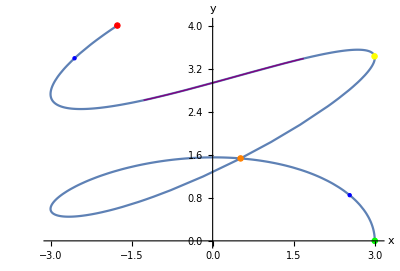

```mathematica
feed = ParametricPlot[Style[r[t], Purple, Thick],{t,0.7,.8}];
Show[track, cauchy, laplace, pont, bale, feed, kmstart, kmend]
```